```mathematica
(* tic tac toe moves, each is position hash, best move, result *)
bestMoves = Partition[{
0,4,0,1,4,0,3,4,0,81,0,0,83,3,0,86,7,0,87,3,0,92,6,0,104,7,5,116,5,2,126,5,0,128,5,2,132,5,2,156,7,5,166,2,0,172,1,0,192,0,0,198,0,0,203,8,-7,205,7,-5,211,6,-8,383,6,-4,384,8,0,389,6,-4,396,1,0,397,8,0,399,7,0,401,7,5,432,8,0,437,8,-7,443,8,-7,624,7,5,828,8,0,833,7,0,857,5,0,900,5,0,905,8,-7,907,7,-5,913,3,0,933,7,-5,1073,1,-1,1109,2,0,1125,0,0,1130,7,0,1139,8,-7,1149,7,-5,1153,3,0,1155,3,0,1163,2,0,1179,0,0,1184,8,-7,1189,2,0,1197,8,0,1210,8,0,1325,2,0,1331,2,8,1341,0,0,1346,8,-6,1347,0,4,1387,3,-2,1418,8,-7,1560,7,5,1788,3,2,1793,3,-4,1839,0,-4,1857,7,5,1893,2,-8,1906,7,-5,2055,7,0,2057,7,5,2066,7,0,2590,8,0,3314,1,-1,3318,0,-1,3368,1,-1,3394,8,0,3396,8,0,3491,2,8,3518,2,-1,3530,1,-1,3543,2,8,3602,8,-7,4174,8,0,4245,2,0,4246,8,0,4250,1,0,4254,0,0,4256,8,9,4330,1,0,7391,1,-1,7528,5,-2,7688,1,-1,7742,1,-1,7768,7,0,8546,7,0,8624,1},3];
```

```mathematica
Length[bestMoves]
```

95

```mathematica
positions = Transpose[bestMoves][[1]];
```

```mathematica
hash[board_] := FromDigits[Reverse[Flatten[board]],3];
dehash[hash_] :=Partition[Reverse[IntegerDigits[hash,3,9]],3]
```

```mathematica
dehash[3]
```

{{0,1,0},{0,0,0},{0,0,0}}

```mathematica
ex = dehash/@ Take[positions,5]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,1}},{{0,0,0},{0,0,0},{0,1,0}},{{0,0,0},{0,1,0},{0,0,0}},{{0,0,0},{0,1,0},{0,0,2}}}

```mathematica
MatrixForm/@ ex
```

{(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1),(0 | 0 | 0
0 | 0 | 0
0 | 1 | 0),(0 | 0 | 0
0 | 1 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 1 | 0
0 | 0 | 2)}

```mathematica
applyPerm[perm_,i_,j_]:= Module[
{pi=i,pj=j,d=IntegerDigits[perm,2,3]},
If[d[[1]]==1,pi=2-pi];
If[d[[2]]==1,pj=2-pj];
If[d[[3]]==1,{pi,pj}={pj,pi}];
Return[{pi,pj}]
]
```

```mathematica
Length[Union[Table[applyPerm[p,a,b],{p,0,7}]]]
```

8

```mathematica
applyPerm[perm_,board_] := Module[
{b=Table[0,{i,0,2},{j,0,2}],i,j,pi,pj},
For[i=0,i<3, i++,
For[j=0,j<3,j++,
{pi,pj}=applyPerm[perm,i,j];
b=ReplacePart[b,{pi+1,pj+1}->board[[i+1]][[j+1]]];
]];
Return[b]
]
```

```mathematica
p100 = dehash[positions[[67]]];
p100//MatrixForm
```

(0 | 0 | 2
1 | 2 | 1
0 | 1 | 0)

```mathematica
applyPerm[3,p100]
```

{{2,1,0},{0,2,1},{0,1,0}}

```mathematica
minHash[board_] := Module[{t,h,mh},
t = Table[{p,applyPerm[p,board]},{p,0,7}];
h = {#[[1]],#[[2]],hash[#[[2]]]}&/@t;
mh = Min[Transpose[h][[2]]];
Return[{mh,h}];
]
```

```mathematica
minHash[p100]
```

{0,{{0,{{0,0,2},{1,2,1},{0,1,0}},1893},{1,{{0,1,0},{0,2,1},{2,1,0}},2397},{2,{{2,0,0},{1,2,1},{0,1,0}},13557},{3,{{2,1,0},{0,2,1},{0,1,0}},15501},{4,{{0,1,0},{1,2,1},{0,0,2}},2621},{5,{{0,1,0},{1,2,0},{0,1,2}},2597},{6,{{0,1,0},{1,2,1},{2,0,0}},2637},{7,{{0,1,2},{1,2,0},{0,1,0}},4053}}}

```mathematica
moves[board_] := Position[board,0]
```

```mathematica
moves[p100]
```

{{1,1},{1,2},{3,1},{3,3}}

```mathematica
depth[board_] := 9-Length[moves[board]]
```

```mathematica
depth[p100]
```

5

```mathematica
toMove[board_] := If[OddQ[depth[board]],2,1]
```

```mathematica
toMove[p100]
```

2

```mathematica
?DirectedEdge
```

```mathematica
full3 = Graph[{DirectedEdge[0,1,0],DirectedEdge[1,7,1],DirectedEdge[7,34,3],DirectedEdge[7,88,4],DirectedEdge[1,55,3],DirectedEdge[55,58,1],DirectedEdge[55,136,4],DirectedEdge[1,163,4],DirectedEdge[163,166,1],DirectedEdge[163,190,3],DirectedEdge[0,3,1],DirectedEdge[3,5,0],DirectedEdge[5,32,3],DirectedEdge[5,86,4],DirectedEdge[3,57,3],DirectedEdge[57,58,0],DirectedEdge[57,138,4],DirectedEdge[3,165,4],DirectedEdge[165,166,0],DirectedEdge[165,192,3],DirectedEdge[0,27,3],DirectedEdge[27,29,0],DirectedEdge[29,32,1],DirectedEdge[29,110,4],DirectedEdge[27,33,1],DirectedEdge[33,34,0],DirectedEdge[33,114,4],DirectedEdge[27,189,4],DirectedEdge[189,190,0],DirectedEdge[189,192,1],DirectedEdge[0,81,4],DirectedEdge[81,83,0],DirectedEdge[83,86,1],DirectedEdge[83,110,3],DirectedEdge[81,87,1],DirectedEdge[87,88,0],DirectedEdge[87,114,3],DirectedEdge[81,135,3],DirectedEdge[135,136,0],DirectedEdge[135,138,1]}];
EdgeCount[full3]
```

40

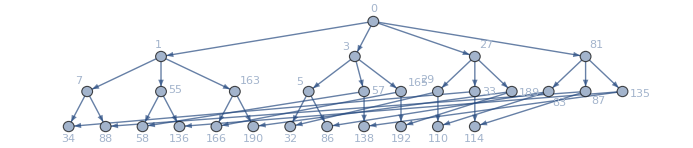

```mathematica
GraphPlot[full3,GraphLayout->"LayeredEmbedding",VertexLabels->"Name"]
```

```mathematica
Table[3^i,{i,0,8}]
```

{1,3,9,27,81,243,729,2187,6561}

```mathematica
minTbl = {{0,4,0},{1,4,0},{3,4,0},{81,0,0},{83,3,0},{86,7,0},{87,3,0},{92,6,0},{104,7,5},{116,5,2},{126,5,0},{128,5,2},{132,5,2},{156,7,5},{166,2,0},{172,1,0},{192,0,0},{198,0,0},{203,8,-7},{205,7,-5},{211,6,-8},{383,6,-4},{384,8,0},{389,6,-4},{396,1,0},{397,8,0},{399,7,0},{401,7,5},{432,8,0},{437,8,-7},{443,8,-7},{624,7,5},{828,8,0},{833,7,0},{857,5,0},{900,5,0},{905,8,-7},{907,7,-5},{913,3,0},{933,7,-5},{1073,1,-1},{1109,2,0},{1125,0,0},{1130,7,0},{1139,8,-7},{1149,7,-5},{1153,3,0},{1155,3,0},{1163,2,0},{1179,0,0},{1184,8,-7},{1189,2,0},{1197,8,0},{1210,8,0},{1325,2,0},{1331,2,8},{1341,0,0},{1346,8,-6},{1347,0,4},{1387,3,-2},{1418,8,-7},{1560,7,5},{1788,3,2},{1793,3,-4},{1839,0,-4},{1857,7,5},{1893,2,-8},{1906,7,-5},{2055,7,0},{2057,7,5},{2066,7,0},{2590,8,0},{3314,1,-1},{3318,0,-1},{3368,1,-1},{3394,8,0},{3396,8,0},{3491,2,8},{3518,2,-1},{3530,1,-1},{3543,2,8},{3602,8,-7},{4174,8,0},{4245,2,0},{4246,8,0},{4250,1,0},{4254,0,0},{4256,8,9},{4330,1,0},{7391,1,-1},{7528,5,-2},{7688,1,-1},{7742,1,-1},{7768,7,0},{8546,7,0},{8624,1,0}};
```

```mathematica
(* see this for nice info "https://community.wolfram.com/groups/-/m/t/2317406" *)
```

```mathematica
boardImage[list_, sz_:30]:=ArrayPlot[list,
ColorRules->{0->White,1->Red,2->Blue,3->Green},
ImageSize->{sz,sz},Mesh->True
(* obsolete PixelConstrained->True *)
];
boardImage[Evaluate[showBest[dehash[#[[1]]],#[[2]]]]]& /@ Select[minTbl,toMove[dehash[#[[1]]]]==1&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
deindex[m_] := {Mod[m,3],Floor[m/3]}
```

```mathematica
showBest[bd_,m_] := ReplacePart[bd,Reverse[deindex[m]]+1->3]
```

```mathematica
showBest[dehash[0],3]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
boardImage[showBest[dehash[0],3]]
```

-Graphics-

```mathematica
imgsAll = boardImage[Evaluate[showBest[dehash[#[[1]]],#[[2]]]]]& /@ minTbl
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[imgsAll]
```

96

```mathematica
gr[imgsAll,12]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
imgsFirst = boardImage[Evaluate[showBest[dehash[#[[1]]],#[[2]]]]]& /@ Select[minTbl,toMove[dehash[#[[1]]]]==1&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[imgsFirst]
```

22

```mathematica
gr[lst_,n_] := Grid[Partition[lst,UpTo[n]]]
```

```mathematica
gr[imgsFirst,6]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |

```mathematica
compFirst = boardImage[Evaluate[showBest[dehash[#[[1]]],#[[2]]]]]& /@ Select[minTbl,toMove[dehash[#[[1]]]]==2&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[compFirst]
```

74

```mathematica
gr[compFirst,11]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |

```mathematica
3^9-1
```

19682

```mathematica
Clear[drawList];
drawList[lst_,n_:10,toMoves_:{1,2}, sz_:30]:=gr[boardImage[Evaluate[showBest[dehash[#[[1]]],#[[2]]]],sz]& /@ Select[lst,MemberQ[toMoves,toMove[dehash[#[[1]]]]]&],n]
```

```mathematica
drawList[minTbl,12, {1,2}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
drawList[minTbl,11, {1}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
FactorInteger[74]
```

{{2,1},{37,1}}

```mathematica
drawList[minTbl,15, {2}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
b765 = {{0,0,-1},{1,4,-1},{3,0,-1},{5,3,-1},{7,3,-1},{11,5,-1},{14,3,-1},{16,4,-1},{32,4,-1},{33,0,-1},{34,2,-1},{38,4,-1},{42,4,-1},{44,4,-1},{45,0,-1},{46,1,-1},{48,8,-1},{50,4,-1},{52,4,-1},{63,0,-1},{64,1,-1},{66,0,-1},{68,4,-1},{70,4,-1},{76,4,-1},{81,0,-1},{83,1,-1},{86,7,-1},{87,0,-1},{88,2,-1},{92,6,-1},{98,3,-1},{104,3,-1},{114,0,-1},{116,2,-1},{125,5,-1},{126,5,-1},{128,1,-1},{131,5,-1},{132,0,-1},{133,5,-1},{142,2,-1},{144,0,-1},{146,6,-1},{149,6,-1},{150,0,-1},{151,5,-1},{154,1,-1},{156,0,-1},{157,5,-1},{163,1,-1},{165,0,-1},{166,2,-1},{172,1,-1},{176,8,-1},{178,7,-1},{192,0,-1},{194,8,-1},{196,6,-1},{198,0,-1},{200,8,-1},{203,8,-1},{204,7,-1},{205,7,-1},{208,6,-1},{210,6,-1},{211,6,-1},{226,1,-1},{228,0,-1},{229,-1,-1},{272,4,-1},{276,4,-1},{278,2,-1},{287,4,-1},{290,4,-1},{293,4,-1},{297,0,-1},{298,2,-1},{300,2,-1},{302,6,-1},{304,8,-1},{306,8,-1},{308,6,-1},{311,6,-1},{312,4,-1},{313,8,-1},{316,1,-1},{318,0,-1},{319,4,-1},{359,-1,-1},{371,-1,-1},{378,0,-1},{380,6,-1},{383,6,-1},{384,2,-1},{385,8,-1},{389,6,-1},{393,0,-1},{395,6,-1},{396,0,-1},{397,8,-1},{399,7,-1},{401,7,-1},{403,8,-1},{432,0,-1},{434,1,-1},{437,2,-1},{438,0,-1},{439,6,-1},{443,8,-1},{449,8,-1},{455,6,-1},{460,2,-1},{462,2,-1},{463,2,-1},{468,0,-1},{469,1,-1},{471,0,-1},{473,8,-1},{475,8,-1},{481,6,-1},{544,2,-1},{550,1,-1},{553,-1,-1},{622,1,-1},{624,0,-1},{625,2,-1},{631,1,-1},{635,6,-1},{637,6,-1},{740,1,-1},{744,4,-1},{746,4,-1},{747,0,-1},{748,1,-1},{750,4,-1},{752,7,-1},{754,3,-1},{773,4,-1},{774,0,-1},{776,1,-1},{779,8,-1},{780,0,-1},{781,-1,-1},{798,4,-1},{799,4,-1},{802,8,-1},{804,7,-1},{805,5,-1},{827,-1,-1},{828,0,-1},{830,1,-1},{833,7,-1},{834,0,-1},{835,3,-1},{857,1,-1},{861,0,-1},{863,-1,-1},{879,-1,-1},{882,7,-1},{883,8,-1},{885,7,-1},{887,7,-1},{889,8,-1},{900,1,-1},{902,8,-1},{905,3,-1},{906,7,-1},{907,3,-1},{910,3,-1},{912,0,-1},{913,3,-1},{933,0,-1},{935,5,-1},{936,0,-1},{937,-1,-1},{939,0,-1},{941,8,-1},{961,5,-1},{967,5,-1},{974,2,-1},{978,4,-1},{980,2,-1},{989,3,-1},{992,1,-1},{995,4,-1},{996,0,-1},{997,3,-1},{1007,2,-1},{1019,1,-1},{1023,0,-1},{1025,-1,-1},{1028,1,-1},{1031,2,-1},{1032,2,-1},{1033,4,-1},{1037,1,-1},{1041,0,-1},{1043,4,-1},{1044,0,-1},{1045,4,-1},{1047,4,-1},{1049,7,-1},{1051,8,-1},{1061,2,-1},{1073,1,-1},{1077,0,-1},{1079,-1,-1},{1109,2,-1},{1113,2,-1},{1115,2,-1},{1124,-1,-1},{1125,0,-1},{1127,1,-1},{1130,7,-1},{1131,0,-1},{1132,8,-1},{1136,8,-1},{1139,8,-1},{1140,7,-1},{1141,7,-1},{1145,8,-1},{1149,7,-1},{1151,8,-1},{1153,3,-1},{1155,0,-1},{1157,8,-1},{1159,3,-1},{1163,1,-1},{1167,0,-1},{1169,2,-1},{1178,7,-1},{1179,0,-1},{1181,1,-1},{1184,8,-1},{1185,0,-1},{1186,-1,-1},{1189,1,-1},{1191,2,-1},{1193,8,-1},{1195,7,-1},{1197,8,-1},{1199,8,-1},{1202,8,-1},{1203,8,-1},{1204,7,-1},{1207,1,-1},{1209,0,-1},{1210,7,-1},{1216,1,-1},{1220,4,-1},{1222,2,-1},{1226,4,-1},{1229,4,-1},{1230,0,-1},{1231,3,-1},{1234,3,-1},{1237,3,-1},{1244,2,-1},{1247,8,-1},{1248,0,-1},{1249,-1,-1},{1253,4,-1},{1257,0,-1},{1259,4,-1},{1260,0,-1},{1261,-1,-1},{1263,8,-1},{1265,8,-1},{1270,4,-1},{1272,4,-1},{1273,2,-1},{1278,4,-1},{1279,4,-1},{1281,4,-1},{1283,4,-1},{1285,4,-1},{1291,4,-1},{1298,1,-1},{1301,2,-1},{1302,0,-1},{1303,2,-1},{1307,-1,-1},{1311,-1,-1},{1315,8,-1},{1319,7,-1},{1321,3,-1},{1325,2,-1},{1329,0,-1},{1331,2,-1},{1340,-1,-1},{1341,0,-1},{1343,1,-1},{1346,8,-1},{1347,0,-1},{1348,-1,-1},{1351,1,-1},{1353,0,-1},{1355,2,-1},{1357,2,-1},{1359,-1,-1},{1364,-1,-1},{1366,-1,-1},{1369,8,-1},{1371,7,-1},{1372,8,-1},{1378,3,-1},{1381,3,-1},{1387,3,-1},{1391,3,-1},{1393,3,-1},{1399,3,-1},{1405,-1,-1},{1407,0,-1},{1409,8,-1},{1415,8,-1},{1418,8,-1},{1419,0,-1},{1420,-1,-1},{1425,0,-1},{1426,-1,-1},{1435,-1,-1},{1441,-1,-1},{1443,-1,-1},{1480,4,-1},{1506,4,-1},{1507,4,-1},{1558,1,-1},{1560,0,-1},{1561,3,-1},{1587,0,-1},{1589,5,-1},{1591,5,-1},{1669,-1,-1},{1704,0,-1},{1706,2,-1},{1708,4,-1},{1712,3,-1},{1715,3,-1},{1716,3,-1},{1717,8,-1},{1720,4,-1},{1722,4,-1},{1723,4,-1},{1730,2,-1},{1733,4,-1},{1734,2,-1},{1735,4,-1},{1739,1,-1},{1743,0,-1},{1745,4,-1},{1746,4,-1},{1747,4,-1},{1749,4,-1},{1751,4,-1},{1753,4,-1},{1758,0,-1},{1759,2,-1},{1765,1,-1},{1767,0,-1},{1769,-1,-1},{1771,8,-1},{1777,4,-1},{1784,3,-1},{1787,3,-1},{1788,0,-1},{1789,2,-1},{1793,3,-1},{1797,0,-1},{1799,3,-1},{1801,1,-1},{1803,0,-1},{1805,3,-1},{1807,3,-1},{1811,-1,-1},{1815,-1,-1},{1826,-1,-1},{1827,-1,-1},{1832,-1,-1},{1834,-1,-1},{1839,0,-1},{1841,-1,-1},{1843,8,-1},{1847,-1,-1},{1851,8,-1},{1852,8,-1},{1855,1,-1},{1857,0,-1},{1858,7,-1},{1866,2,-1},{1867,2,-1},{1873,1,-1},{1875,0,-1},{1877,8,-1},{1879,8,-1},{1885,-1,-1},{1893,0,-1},{1895,2,-1},{1897,2,-1},{1901,8,-1},{1904,8,-1},{1905,8,-1},{1906,7,-1},{1909,-1,-1},{1911,-1,-1},{1921,2,-1},{1927,1,-1},{1929,0,-1},{1930,-1,-1},{1948,2,-1},{1954,1,-1},{1957,-1,-1},{1974,2,-1},{1975,2,-1},{1981,1,-1},{1983,0,-1},{1985,4,-1},{1987,4,-1},{1993,4,-1},{2029,2,-1},{2035,1,-1},{2039,7,-1},{2041,8,-1},{2047,7,-1},{2055,7,-1},{2057,7,-1},{2059,8,-1},{2063,1,-1},{2066,7,-1},{2067,0,-1},{2068,8,-1},{2071,8,-1},{2073,7,-1},{2074,8,-1},{2083,2,-1},{2089,1,-1},{2091,0,-1},{2092,-1,-1},{2137,2,-1},{2143,1,-1},{2145,0,-1},{2146,-1,-1},{2465,2,-1},{2477,1,-1},{2483,-1,-1},{2490,8,-1},{2491,8,-1},{2495,6,-1},{2499,8,-1},{2501,6,-1},{2503,4,-1},{2505,4,-1},{2507,4,-1},{2509,8,-1},{2571,0,-1},{2573,2,-1},{2582,6,-1},{2585,1,-1},{2588,-1,-1},{2589,0,-1},{2590,8,-1},{2625,0,-1},{2627,2,-1},{2636,8,-1},{2639,1,-1},{2642,6,-1},{2653,8,-1},{2657,8,-1},{2660,6,-1},{2661,8,-1},{2662,8,-1},{2665,6,-1},{2667,6,-1},{2668,6,-1},{2730,4,-1},{2731,4,-1},{2737,4,-1},{2741,4,-1},{2743,4,-1},{2811,-1,-1},{2815,2,-1},{2819,1,-1},{2822,-1,-1},{2824,6,-1},{2893,-1,-1},{2899,-1,-1},{3179,1,-1},{3185,-1,-1},{3230,4,-1},{3233,1,-1},{3236,4,-1},{3237,8,-1},{3238,8,-1},{3314,1,-1},{3318,0,-1},{3320,-1,-1},{3338,8,-1},{3341,8,-1},{3344,8,-1},{3346,3,-1},{3368,1,-1},{3372,0,-1},{3374,-1,-1},{3390,8,-1},{3392,8,-1},{3394,8,-1},{3396,8,-1},{3398,8,-1},{3400,8,-1},{3407,2,-1},{3409,2,-1},{3413,1,-1},{3419,3,-1},{3421,8,-1},{3425,4,-1},{3427,3,-1},{3435,0,-1},{3437,2,-1},{3446,4,-1},{3449,8,-1},{3452,8,-1},{3453,0,-1},{3454,-1,-1},{3461,4,-1},{3463,4,-1},{3467,4,-1},{3470,4,-1},{3471,4,-1},{3472,4,-1},{3475,8,-1},{3477,4,-1},{3478,4,-1},{3491,2,-1},{3500,-1,-1},{3503,1,-1},{3506,-1,-1},{3508,8,-1},{3518,2,-1},{3530,1,-1},{3534,0,-1},{3536,-1,-1},{3542,-1,-1},{3543,0,-1},{3544,2,-1},{3548,-1,-1},{3552,-1,-1},{3556,8,-1},{3558,-1,-1},{3562,8,-1},{3569,8,-1},{3571,3,-1},{3575,8,-1},{3578,3,-1},{3580,3,-1},{3583,3,-1},{3586,3,-1},{3596,8,-1},{3597,0,-1},{3598,-1,-1},{3602,8,-1},{3606,0,-1},{3608,8,-1},{3610,-1,-1},{3614,8,-1},{3632,-1,-1},{3634,-1,-1},{3640,-1,-1},{3907,4,-1},{3911,4,-1},{3913,4,-1},{3938,4,-1},{3939,4,-1},{3940,4,-1},{3989,1,-1},{3992,-1,-1},{3994,3,-1},{4020,-1,-1},{4048,8,-1},{4069,-1,-1},{4100,-1,-1},{4102,-1,-1},{4141,1,-1},{4145,4,-1},{4147,3,-1},{4153,4,-1},{4163,4,-1},{4165,2,-1},{4169,1,-1},{4172,4,-1},{4173,0,-1},{4174,4,-1},{4177,1,-1},{4180,4,-1},{4195,1,-1},{4198,-1,-1},{4219,8,-1},{4223,1,-1},{4226,-1,-1},{4228,8,-1},{4231,1,-1},{4234,-1,-1},{4244,-1,-1},{4245,0,-1},{4246,8,-1},{4250,1,-1},{4254,0,-1},{4256,8,-1},{4258,8,-1},{4264,8,-1},{4276,1,-1},{4282,8,-1},{4303,1,-1},{4306,-1,-1},{4330,1,-1},{4334,8,-1},{4336,8,-1},{4342,-1,-1},{5005,1,-1},{5008,-1,-1},{5599,1,-1},{5603,4,-1},{5605,3,-1},{5611,3,-1},{5630,4,-1},{5632,-1,-1},{5638,-1,-1},{5684,-1,-1},{5686,-1,-1},{5689,3,-1},{5692,8,-1},{5716,-1,-1},{5720,8,-1},{5746,8,-1},{5761,1,-1},{5764,-1,-1},{5792,8,-1},{6448,8,-1},{7307,3,-1},{7310,7,-1},{7313,7,-1},{7337,1,-1},{7343,-1,-1},{7361,4,-1},{7363,1,-1},{7367,7,-1},{7369,4,-1},{7391,1,-1},{7397,-1,-1},{7442,-1,-1},{7445,7,-1},{7448,7,-1},{7450,-1,-1},{7463,1,-1},{7469,5,-1},{7475,7,-1},{7496,7,-1},{7499,7,-1},{7502,7,-1},{7504,-1,-1},{7522,5,-1},{7525,7,-1},{7528,5,-1},{7604,-1,-1},{7607,7,-1},{7610,7,-1},{7612,4,-1},{7688,1,-1},{7694,-1,-1},{7742,1,-1},{7748,-1,-1},{7760,-1,-1},{7768,7,-1},{7772,7,-1},{7774,7,-1},{7841,4,-1},{7844,4,-1},{7846,4,-1},{7922,-1,-1},{7934,7,-1},{8006,-1,-1},{8008,-1,-1},{8038,4,-1},{8041,4,-1},{8069,4,-1},{8071,4,-1},{8119,-1,-1},{8123,3,-1},{8150,5,-1},{8152,-1,-1},{8203,-1,-1},{8273,-1,-1},{8285,3,-1},{8287,4,-1},{8306,-1,-1},{8309,4,-1},{8312,4,-1},{8314,4,-1},{8332,-1,-1},{8335,4,-1},{8338,4,-1},{8360,-1,-1},{8363,3,-1},{8366,3,-1},{8368,-1,-1},{8390,-1,-1},{8416,-1,-1},{8420,-1,-1},{8438,-1,-1},{8440,-1,-1},{8462,-1,-1},{8474,-1,-1},{8476,-1,-1},{8500,-1,-1},{8519,3,-1},{8521,4,-1},{8543,1,-1},{8546,4,-1},{8548,4,-1},{8554,4,-1},{8572,-1,-1},{8597,3,-1},{8600,3,-1},{8602,-1,-1},{8624,1,-1},{8630,7,-1},{8636,7,-1},{8654,-1,-1},{8708,7,-1},{8710,7,-1},{8716,-1,-1},{9794,-1,-1},{9953,-1,-1},{9959,-1,-1},{9961,-1,-1},{10115,-1,-1},{10121,-1,-1},{10469,1,-1},{10472,3,-1},{10502,-1,-1},{10528,4,-1},{10550,1,-1},{10556,-1,-1},{10609,-1,-1},{10634,-1,-1},{10706,3,-1},{10736,4,-1},{10742,4,-1},{10744,4,-1},{10760,-1,-1},{10762,4,-1},{10768,4,-1},{10790,3,-1},{10817,-1,-1},{10820,1,-1},{10823,-1,-1},{10825,-1,-1},{10843,-1,-1},{10849,-1,-1},{10868,3,-1},{10895,-1,-1},{10897,-1,-1},{12220,4,-1},{12301,-1,-1},{17060,4,-1},{17141,-1,-1}};
```

```mathematica
FactorInteger[765]
```

{{3,2},{5,1},{17,1}}

```mathematica
Length[b765]
```

765

```mathematica
(* all boards *)
drawList[b765,17*3,{1,2},15]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
FactorInteger[153]
```

{{3,2},{17,1}}

```mathematica
wids={1,3,12,19,18,29,17,17,19,5};
b765Lev = Table[({drawList[#,wids[[d+1]],{1,2},18],Length[#]}&)[Select[b765,depth[dehash[#[[1]]]]==d&]],{d,0,9}]
```

{{-Graphics-,1},{-Graphics- | -Graphics- | -Graphics-,3},{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,12},{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,38},{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,108},{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,174},{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,204},{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,153},{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,57},{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,15}}

```mathematica
dir = NotebookDirectory[]<>"imgs\\"
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\

```mathematica
Export[NotebookDirectory[]<>"tbl765-"<>ToString[#[[2]]]<>".png",#[[1]]]& /@ b765Lev
```

{C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-1.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-3.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-12.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-38.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-108.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-174.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-204.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-153.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-57.png,C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\tbl765-15.png}

```mathematica
b56 = {{0,0,0},{1,1,0},{10895,-1,9},{10897,-1,9},{11,6,0},{1189,3,0},{1195,5,0},{1207,5,0},{1222,3,4},{1234,3,4},{1249,-1,9},{1261,-1,9},{1357,6,8},{1366,-1,9},{1378,1,1},{1405,-1,9},{151,5,0},{163,2,0},{172,1,0},{178,7,0},{1954,2,0},{2041,6,8},{226,3,4},{229,-1,9},{2662,6,0},{3394,5,0},{3400,8,9},{4336,6,9},{550,3,4},{553,-1,9},{63,2,0},{637,6,8},{64,2,0},{7,6,0},{70,4,0},{7310,3,4},{7363,3,0},{7369,4,7},{7450,-1,9},{747,2,0},{748,1,0},{7525,3,4},{754,3,4},{781,-1,9},{7841,5,6},{802,8,0},{8273,-1,9},{8440,-1,9},{8521,4,8},{8572,-1,9},{8602,-1,9},{8708,5,9},{889,8,7},{910,3,4},{937,-1,9},{9961,-1,9}};
Length[b56]
```

56

```mathematica
d56 = drawList[b56,14,{1,2},18]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[dir<>"ttt_56.png",d56]
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\ttt_56.png

```mathematica
b30 = {{0,-1,9},{11,-1,9},{1195,-1,9},{1207,-1,9},{1222,-1,9},{1234,-1,9},{1285,-1,9},{1378,-1,9},{1393,-1,9},{163,-1,9},{178,-1,9},{1954,-1,9},{226,-1,9},{3400,-1,9},{4336,-1,9},{550,-1,9},{5605,-1,9},{63,-1,9},{7,-1,9},{70,-1,9},{7310,-1,9},{7369,-1,9},{747,-1,9},{7525,-1,9},{754,-1,9},{7841,-1,9},{802,-1,9},{8521,-1,9},{8708,-1,9},{910,-1,9}};
Length[b30]
```

30

```mathematica
d30 = drawList[b30,15,{1,2},18]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[dir<>"ttt_30.png",d30]
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\ttt_30.png

```mathematica
b94 = {{0,1,0},{104,7,5},{10736,4,9},{10817,-1,9},{10895,-1,9},{10897,-1,9},{116,7,5},{1210,5,0},{1244,6,0},{1248,2,1},{1249,-1,9},{1260,6,4},{1261,-1,9},{128,7,5},{1340,-1,9},{1364,-1,9},{1399,3,4},{1405,-1,9},{1426,-1,9},{1480,4,0},{156,2,0},{1560,2,0},{1561,3,0},{157,2,0},{1591,8,7},{165,0,0},{166,2,0},{1712,6,4},{1716,6,4},{176,6,0},{1811,-1,9},{1855,8,7},{1948,6,4},{1957,-1,9},{196,6,4},{1981,2,0},{1987,7,0},{2039,5,2},{2047,7,5},{2059,8,7},{2063,2,0},{2071,8,7},{208,6,4},{2143,3,4},{2146,-1,9},{228,2,1},{229,-1,9},{297,0,0},{3,0,0},{306,1,0},{308,6,4},{312,6,4},{33,0,0},{34,2,0},{359,-1,9},{371,-1,9},{396,6,0},{397,2,0},{403,8,7},{4174,4,0},{4219,8,7},{4226,-1,9},{4234,-1,9},{4336,6,9},{45,0,0},{46,1,0},{468,2,1},{5,4,0},{52,6,4},{544,6,4},{553,-1,9},{5611,3,4},{5638,-1,9},{5684,-1,9},{635,8,7},{7499,3,4},{76,4,0},{7607,3,4},{781,-1,9},{8152,-1,9},{8273,-1,9},{8363,7,5},{8390,-1,9},{8416,-1,9},{8438,-1,9},{86,2,0},{8624,3,0},{8630,5,9},{8708,5,9},{913,3,0},{936,2,1},{937,-1,9},{967,7,0},{9794,-1,9}};
Length[b94]
```

94

```mathematica
d94 = drawList[b94,16,{1,2},18]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |

```mathematica
Export[dir<>"ttt_94.png",d94]
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\ttt_94.png

```mathematica
b51 = {{0,-1,9},{104,-1,9},{1115,-1,9},{1127,-1,9},{116,-1,9},{128,-1,9},{132,-1,9},{1331,-1,9},{1347,-1,9},{1399,-1,9},{1480,-1,9},{156,-1,9},{1560,-1,9},{1591,-1,9},{165,-1,9},{1712,-1,9},{176,-1,9},{1788,-1,9},{1843,-1,9},{1855,-1,9},{1948,-1,9},{196,-1,9},{2047,-1,9},{2063,-1,9},{2071,-1,9},{208,-1,9},{2143,-1,9},{228,-1,9},{297,-1,9},{308,-1,9},{33,-1,9},{3491,-1,9},{3543,-1,9},{380,-1,9},{384,-1,9},{396,-1,9},{403,-1,9},{4219,-1,9},{4256,-1,9},{4336,-1,9},{45,-1,9},{468,-1,9},{5,-1,9},{52,-1,9},{624,-1,9},{7499,-1,9},{8363,-1,9},{8636,-1,9},{8708,-1,9},{936,-1,9},{967,-1,9}};
Length[b51]
```

51

```mathematica
d51 = drawList[b51,17,{1,2},18]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[dir<>"ttt_51.png",d51]
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\ttt_51.png

```mathematica
b41={{0,4,0},{10817,-1,9},{1298,8,7},{1307,-1,9},{1311,-1,9},{1319,3,2},{1359,-1,9},{142,8,7},{146,8,7},{150,8,7},{154,8,7},{1558,8,7},{1797,2,0},{1799,5,2},{1826,-1,9},{1851,6,4},{2039,5,2},{2063,2,0},{2091,5,2},{3506,-1,9},{3558,-1,9},{4226,-1,9},{5716,-1,9},{622,8,7},{81,0,0},{8119,-1,9},{8123,3,2},{827,-1,9},{83,2,0},{830,5,0},{833,1,0},{8390,-1,9},{8624,3,0},{8630,5,9},{87,0,0},{879,-1,9},{88,2,0},{882,3,0},{887,3,2},{92,1,0},{98,8,7}};
Length[b41]
```

41

```mathematica
d41 = drawList[b41,14,{1,2},18]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Export[dir<>"ttt_41.png",d41]
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\ttt_41.png

```mathematica
b22={{0,-1,9},{1298,-1,9},{1302,-1,9},{1319,-1,9},{1321,-1,9},{146,-1,9},{150,-1,9},{2041,-1,9},{2063,-1,9},{2089,-1,9},{5689,-1,9},{622,-1,9},{7445,-1,9},{8123,-1,9},{83,-1,9},{830,-1,9},{834,-1,9},{8630,-1,9},{87,-1,9},{882,-1,9},{887,-1,9},{889,-1,9}};
Length[b22]
```

22

```mathematica
d22 = drawList[b22,11,{1,2},18]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[dir<>"ttt_22.png",d22]
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\ttt_22.png

```mathematica
b127={{0,0,0},{1,4,0},{10634,-1,9},{1073,1,0},{1079,-1,9},{10817,-1,9},{10895,-1,9},{10897,-1,9},{1109,8,0},{1125,2,0},{1127,3,0},{1130,3,0},{1139,6,-8},{1149,7,-5},{1153,3,0},{1163,6,-8},{1179,2,0},{1181,3,0},{1184,6,-8},{1189,6,0},{1197,6,0},{1207,3,0},{1210,8,0},{126,7,0},{1325,8,0},{1341,2,-6},{1343,3,0},{1346,3,0},{1387,7,-5},{1415,2,0},{1418,2,-8},{1435,-1,9},{1441,-1,9},{1443,-1,9},{163,1,0},{165,0,0},{166,2,0},{1669,-1,9},{172,1,0},{176,3,0},{178,3,0},{1793,5,-6},{1839,0,-4},{1841,-1,9},{1847,-1,9},{1885,-1,9},{1893,8,-7},{1904,6,-8},{1906,7,-5},{1909,-1,9},{1911,-1,9},{192,2,0},{198,2,0},{200,1,0},{203,6,-8},{205,6,0},{2055,3,0},{2063,2,0},{2066,5,0},{210,2,0},{211,6,-8},{2589,2,0},{2590,8,0},{3,4,0},{3314,5,-6},{3318,2,-6},{3320,-1,9},{3368,6,-8},{3394,6,0},{3518,8,-6},{3530,5,-6},{3536,-1,9},{3602,2,-8},{3640,-1,9},{380,0,0},{383,6,-4},{389,8,-6},{396,2,0},{397,8,0},{399,7,0},{4069,-1,9},{4245,2,0},{4246,8,0},{4250,3,0},{4254,2,0},{4256,6,9},{432,0,0},{434,2,0},{437,8,-7},{443,6,-8},{5720,2,9},{7391,5,-6},{7397,-1,9},{7502,3,0},{7528,5,0},{7688,5,-6},{7694,-1,9},{7742,5,-6},{7748,-1,9},{7768,3,0},{8006,-1,9},{81,0,0},{8203,-1,9},{828,2,0},{83,1,0},{830,1,0},{833,3,0},{8420,-1,9},{8474,-1,9},{8500,-1,9},{857,7,0},{86,7,0},{8624,3,0},{8630,5,9},{8708,5,9},{8710,7,9},{8716,-1,9},{900,1,0},{905,6,-8},{906,2,0},{907,7,-5},{913,3,0},{92,8,0},{933,7,-5},{939,2,0},{941,3,0},{967,5,0}};
Length[b127]
```

127

```mathematica
d127 = drawList[b127,16,{1,2},18]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Export[dir<>"ttt_127.png",d127]
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\ttt_127.png

```mathematica
b75={{1,-1,9},{1073,-1,9},{10817,-1,9},{10895,-1,9},{10897,-1,9},{1109,-1,9},{1125,-1,9},{1130,-1,9},{1139,-1,9},{1149,-1,9},{1153,-1,9},{1155,-1,9},{1163,-1,9},{1179,-1,9},{1184,-1,9},{1189,-1,9},{1197,-1,9},{1210,-1,9},{126,-1,9},{1325,-1,9},{1341,-1,9},{1346,-1,9},{1387,-1,9},{1418,-1,9},{166,-1,9},{172,-1,9},{1793,-1,9},{1839,-1,9},{1893,-1,9},{1906,-1,9},{192,-1,9},{198,-1,9},{203,-1,9},{205,-1,9},{2055,-1,9},{2066,-1,9},{211,-1,9},{2590,-1,9},{3,-1,9},{3314,-1,9},{3318,-1,9},{3368,-1,9},{3394,-1,9},{3396,-1,9},{3518,-1,9},{3530,-1,9},{3602,-1,9},{383,-1,9},{389,-1,9},{397,-1,9},{399,-1,9},{4246,-1,9},{4250,-1,9},{4254,-1,9},{432,-1,9},{4330,-1,9},{437,-1,9},{443,-1,9},{7391,-1,9},{7528,-1,9},{7688,-1,9},{7742,-1,9},{7768,-1,9},{81,-1,9},{828,-1,9},{833,-1,9},{857,-1,9},{86,-1,9},{8624,-1,9},{900,-1,9},{905,-1,9},{907,-1,9},{913,-1,9},{92,-1,9},{933,-1,9}};
Length[b75]
```

75

```mathematica
d75 = drawList[b75,15,{1,2},18]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[dir<>"ttt_75.png",d75]
```

C:\Users\Chris\OneDrive\Desktop\LomontTicTacToe\imgs\ttt_75.png